-Graphics3D-

Final position after s = 10: {{11.,0.,0.}}

-Graphics3D-

-Graphics3D-

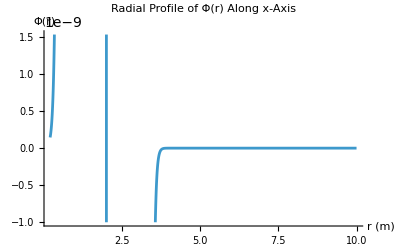

```mathematica
(* ::Title::*)(*Geodesic Traversal and Traversability Check in a 3+1D Wormhole Metric (Optimized Parameters)*)(* ::Section::*)(*Define Parameters and Potential*)R0=2.0;
A=0.01;
w=0.2 R0;
ε=0.04 R0;

ΦSafe[x_,y_,z_]:=Module[{r},r=Max[Sqrt[x^2+y^2+z^2],ε];
-A (1-R0/r) Exp[-(r-R0)^2/w^2]];

(* ::Section::*)(*Define the Metric Components*)

f[x_,y_,z_]:=Exp[2 ΦSafe[x,y,z]];
invf[x_,y_,z_]:=Exp[-2 ΦSafe[x,y,z]];

(* ::Section::*)(*Define the Lagrangian for Geodesic Motion*)

Clear[t,x,y,z,s];

L=-f[x[s],y[s],z[s]] t'[s]^2+invf[x[s],y[s],z[s]] (x'[s]^2+y'[s]^2+z'[s]^2);

(* ::Section::*)(*Compute Euler-Lagrange Equations*)

eqt=D[D[L,t'[s]],s]-D[L,t[s]]==0;
eqx=D[D[L,x'[s]],s]-D[L,x[s]]==0;
eqy=D[D[L,y'[s]],s]-D[L,y[s]]==0;
eqz=D[D[L,z'[s]],s]-D[L,z[s]]==0;

(* ::Section::*)(*Initial Conditions and Numerical Integration for Timelike Geodesic*)

timelikeIC={t[0]==0,x[0]==0.5 R0,y[0]==0,z[0]==0,t'[0]==1,x'[0]==1,y'[0]==0,z'[0]==0};

timelikeSol=NDSolve[{eqt,eqx,eqy,eqz}~Join~timelikeIC,{t,x,y,z},{s,0,10},MaxStepFraction->1/100];

(* ::Section::*)(*Plot the Geodesic Path (3D)*)

ParametricPlot3D[Evaluate[{x[s],y[s],z[s]}/. timelikeSol],{s,0,10},PlotRange->All,AxesLabel->{"x (m)","y (m)","z (m)"},PlotLabel->"Timelike Geodesic Path Through Wormhole (Optimized Parameters)"]

(* ::Section::*)(*Output Final Position*)

Print["Final position after s = 10: ",{x[10],y[10],z[10]}/. timelikeSol];

(* ::Section::*)(*Null Geodesic Case*)

Lnull=L;

eqtN=eqt;
eqxN=eqx;
eqyN=eqy;
eqzN=eqz;

nullIC={t[0]==0,x[0]==0.5 R0,y[0]==0,z[0]==0,t'[0]==1,x'[0]==1,y'[0]==0,z'[0]==0};

nullSol=NDSolve[{eqtN,eqxN,eqyN,eqzN}~Join~nullIC,{t,x,y,z},{s,0,10},MaxStepFraction->1/100];

ParametricPlot3D[Evaluate[{x[s],y[s],z[s]}/. nullSol],{s,0,10},PlotRange->All,AxesLabel->{"x (m)","y (m)","z (m)"},PlotLabel->"Null Geodesic Path Through Wormhole"]

(* ::Section::*)(*Animated Traversal (Timelike Geodesic)*)

frames3D=Table[Graphics3D[{Red,PointSize[Large],Point[{x[s],y[s],z[s]}/. timelikeSol]},PlotRange->{{-3 R0,12 R0},{-3 R0,3 R0},{-3 R0,3 R0}},Axes->True,AxesLabel->{"x (m)","y (m)","z (m)"},BoxRatios->{4,1,1}],{s,0,10,0.5}];

ListAnimate[frames3D]

(* ::Section::*)(*Potential Visualization (Equatorial Plane z=0)*)

Plot3D[ΦSafe[x,y,0],{x,-3 R0,3 R0},{y,-3 R0,3 R0},PlotLabel->"Scalar Potential Φ(x,y,z=0)",AxesLabel->{"x (m)","y (m)","Φ"},PlotRange->All,PlotPoints-> 200,MaxRecursion->8,Mesh->None]

(*Optional radial potential plot*)

Plot[ΦSafe[r,0,0],{r,0.1 R0,5 R0},PlotLabel->"Radial Profile of Φ(r) Along x-Axis",AxesLabel->{"r (m)","Φ(r)"}]
```